# NSTX ECH with Parabolic/toroid Profiles

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx^2 from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

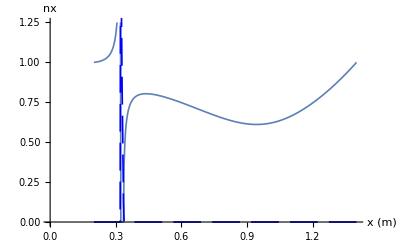

dataSet=Slab 90HHz

n0=5.×10^19

b0=1.

freq=90000

rMaj=1.

rOut=1.4

κ=1.1

ι0=0.00001

α1=1.

α2=1.

αT1=1.

αT2=2.

t0=1.

nz=0.05

etaList={0.,1.,0.,0.,0.}

xmin=0.2

xmax=1.4

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
myComplexListPlot[nt,"x (m)","nx"]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots)

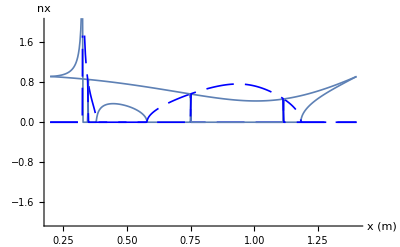

dataSet=Slab 90HHz

n0=7.5×10^19

b0=1.

freq=90000

rMaj=1.

rOut=1.4

κ=1.1

ι0=0.00001

α1=1.

α2=1.

αT1=1.

αT2=2.

t0=1.

nz=0.4

etaList={0.,1.,0.,0.,0.}

xmin=0.2

xmax=1.4

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (m)","nx"];
g2=myComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

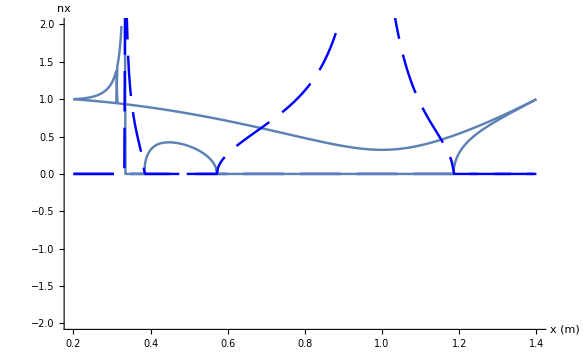

dataSet=Slab 90HHz

n0=9.×10^19

b0=1.

freq=90000

rMaj=1.

rOut=1.4

κ=1.1

ι0=0.01

α1=1.

α2=2.

αT1=2.

αT2=1.

t0=1.

nz=0.03

etaList={0.,1.,0.,0.,0.}

xmin=0.2

xmax=1.4

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2PM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=myComplexListPlot[nP,"x (m)","nx"];
g2=myComplexListPlot[nM,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

```mathematica
nPerp2FS[x_]
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

dataSet=DIII-D slab

xProfileMin=-0.68

xProfileMax=0.68

nXmin=2.5×10^19

nXmax=3.5×10^19

BXmin=1.9

BXmax=2.1

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=-0.68

xmax=0.68

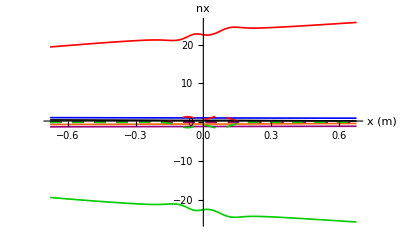

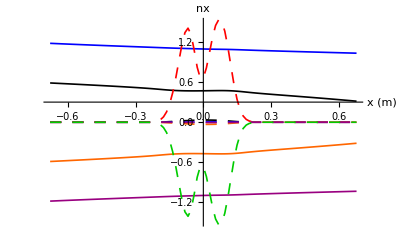

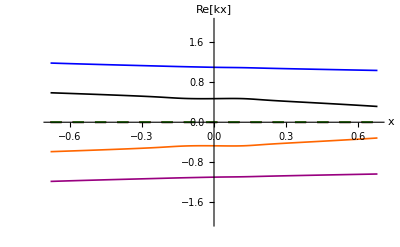

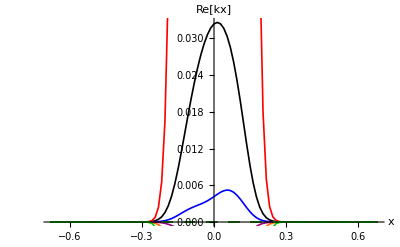

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-1.5,1.5}]
ComplexVectorListPlot[rootsRe, "x", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "x", "Re[kx]"]
```

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
nPerpHot[x_,nxGuess_]:=Module[{ne,b,x0,TL,nx0},
		x0=x;
nx0=nxGuess;
     ne=nprof[x0];
b=bprof[x0];
     TL=tprof[x0]*TList;
rootRule=FindRoot[DisFuncGeneral[freq,ne,b,nz,nx,etaList,TL,nminList,nmaxList,modelList],{nx,nx0}, MaxIterations->30];
nx/.rootRule]
```

### First try root finding on warm plasma dispersion rel (model = 1)

```mathematica
modelList =Table[1,{i,1,6}];
```

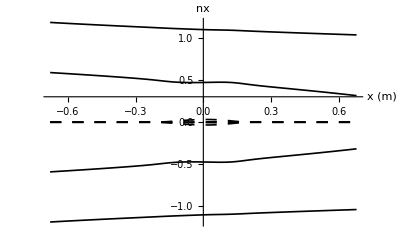

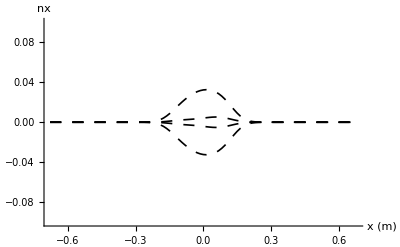

dataSet=DIII-D slab

ne0=ne0

nsep=nsep

B=B

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,1,1,1,1}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g10,g11},PlotRange->All]
Show[{g7,g8,g10,g11},PlotRange->{-.1,.1}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

#### Now try with hot plasma (model = 2) for all species. Can I find the warm plasma roots with the full dispersion relation?

```mathematica
xPoint=0.;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.472427+0.0323801 ⅈ,1.10079+0.00415331 ⅈ,22.5351+0.667857 ⅈ,-0.472427-0.0323801 ⅈ,-1.10079-0.00415331 ⅈ,-22.5351-0.667857 ⅈ}

Change model to 2

```mathematica
modelList =Table[2,{i,1,6}];
```

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

{0.590246+1.7869×10^-27 ⅈ,1.18681+3.41307×10^-28 ⅈ,1.18681+7.67968×10^-26 ⅈ,-0.590246-1.7869×10^-27 ⅈ,-1.18681-3.41307×10^-28 ⅈ,-1.18681-7.67968×10^-26 ⅈ}

dataSet=DIII-D slab

ne0=ne0

nsep=nsep

B=B

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,2,2,2,2}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

Hot plasma root finder gets all roots.  What about at xmin?

```mathematica
xPoint=xmin;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.590188,1.18597,19.3865,-0.590188,-1.18597,-19.3865}

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

{0.590246+1.7869×10^-27 ⅈ,1.18681+3.41307×10^-28 ⅈ,1.18681+7.67968×10^-26 ⅈ,-0.590246-1.7869×10^-27 ⅈ,-1.18681-3.41307×10^-28 ⅈ,-1.18681-7.67968×10^-26 ⅈ}

dataSet=DIII-D slab

ne0=ne0

nsep=nsep

B=B

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

Hot plasma root finder gets 2 of the roots

### Plot hot plasma vs x

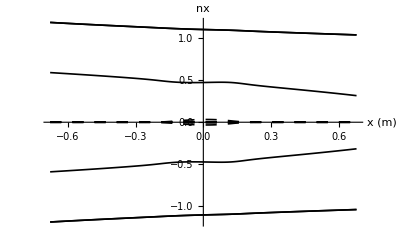

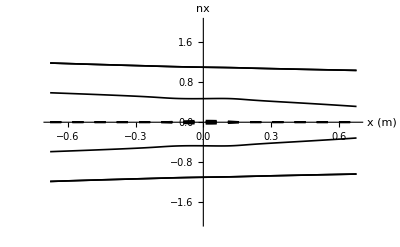

dataSet=DIII-D slab

ne0=ne0

nsep=nsep

B=B

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

```mathematica
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g7,g8,g9,g10,g11,g12},PlotRange->{-2.,2.},AxesOrigin->{0.,0.}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

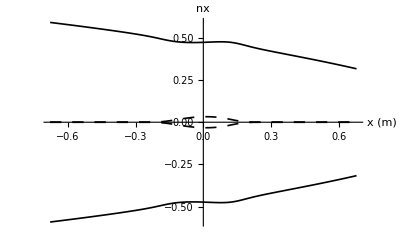

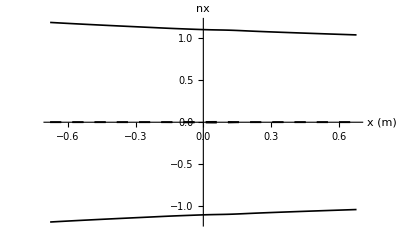

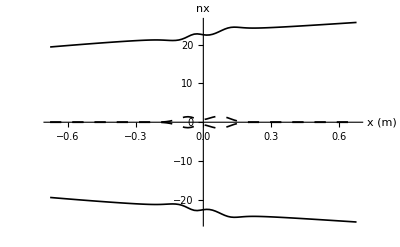

```mathematica
Show[{g7,g10},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g8,g11},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g9,g12},PlotRange->All,AxesOrigin->{0.,0.}]
```

## Focus on the damping

```mathematica
nxhotIm[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,Im[nPerpHot[x0,nxGuess]]};),{i,1,nPoints}];
nxH];
```

#### X - mode

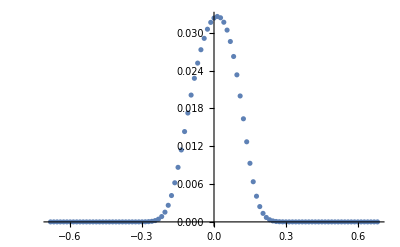

```mathematica
ListPlot[nxhotIm[1],PlotRange->All]
```

### O - mode

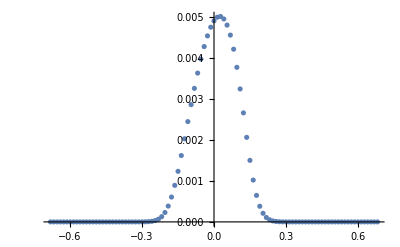

```mathematica
ListPlot[nxhotIm[2],PlotRange->All]
```

## Plot Profiles

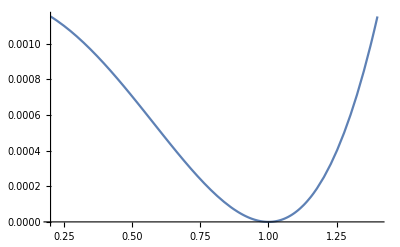

```mathematica
Plot[ψ[x,0.,rMaj,b0,ι0,κ],{x,xmin,xmax}]
```

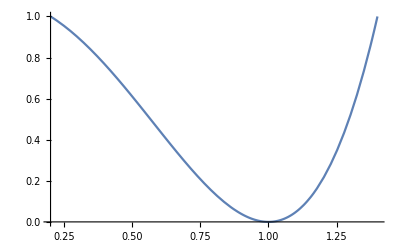

```mathematica
Plot[ψN[x,0.,rMaj,rOut,b0,ι0,κ],{x,xmin,xmax}]
```

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

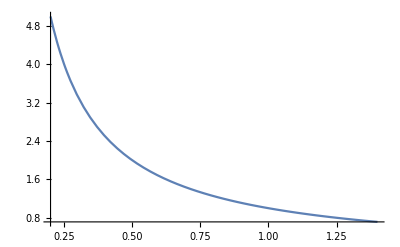

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

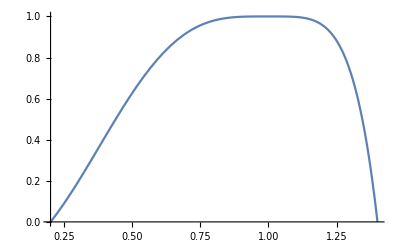

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[BXmax,freq, nz,1]
```

0.96×1.00005

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
ψ0[b0_, ι0_]:=b0 ι0/2.
ψ[r_,z_,rMaj_,b0_,ι0_,κ_]:=ψ0[b0, ι0](r^2/rMaj^2 z^2/κ^2+((r^2-rMaj^2)^2)/(4 rMaj^2))
ψB[rMaj_,rOut_,b0_,ι0_,κ_]:=ψ[rOut,0.,rMaj,b0,ι0,κ]
ψN[r_,z_,rMaj_,rOut_,b0_,ι0_,κ_]:=ψ[r,z,rMaj,b0,ι0,κ]/ψB[rMaj,rOut,b0,ι0,κ]
```

```mathematica
bprof[x_]:=b0 rMaj/x
```

```mathematica
nprof[x_]:=If[ψN[x,0.,rMaj,rOut,b0,ι0,κ]<1.,n0(1-ψN[x,0.,rMaj,rOut,b0,ι0,κ]^α2)^α1,0.]
```

```mathematica
tprof[x_]:=If[ψN[x,0.,rMaj,rOut,b0,ι0,κ]<1.,t0(1-ψN[x,0.,rMaj,rOut,b0,ι0,κ]^αT2)^αT1,0.]
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```